```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/hybrid_tail/math

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
Normal[Series[ηr[ϕc(1+ζ),0],{ζ,0,1}]]//Simplify
```

(8 ζ)/M^2

```mathematica
Solve[(8ζ)/M^2==-2,ζ]
```

{{ζ→-M^2/4}}

```mathematica
N1s=NN/.Solve[-Π2/4==-NN,NN][[1]]//Simplify
```

Π2/4

```mathematica
N2s=dN/.Solve[Normal[Series[-Π2/4==-(N1+dN)-(N1+dN)^2/μ2^2,{dN,0,1}]],dN][[1]]/.{Π2->8N1}//Simplify
```

(N1 (-N1+μ2^2))/(2 N1+μ2^2)

```mathematica
N3s=dN/.Solve[Normal[Series[-Π2/4==-(N1+N2+dN)-(N1+N2+dN)^2/μ2^2-ϕc/μ3^3 1/(μ1 ϕc)(N1+N2+dN)^3,{dN,0,1}]],dN][[1]]/.{Π2->8N1}//Simplify
```

-(-N1+N2+(N1+N2)^2/μ2^2+(N1+N2)^3/(μ1 μ3^3))/(1+(2 (N1+N2))/μ2^2+(3 (N1+N2)^2)/(μ1 μ3^3))

```mathematica
Normal[Series[Sinh[x],{x,0,1}]]
```

x

```mathematica
Sinh[x]//TrigToExp
```

-ⅇ^-x/2+ⅇ^x/2

```mathematica
PDF[JohnsonDistribution["SU",γ,δ,μ,σ],𝒩]
```

(ⅇ^(-1/2 (γ+δ ArcSinh[(𝒩-μ)/σ])^2) δ)/(√(2 π) √((𝒩-μ)^2+σ^2))

```mathematica
Mean[JohnsonDistribution["SU",γ,δ,μ,σ]]/(μ-σ Exp[δ^-2/2]Sinh[γ/δ])//Simplify
```

1

```mathematica
𝒟[𝒩_]=-D[Log[PDF[JohnsonDistribution["SU",γ,δ,μ,σ],𝒩]], 𝒩]//FullSimplify
```

(𝒩-μ+γ δ √(1+(𝒩-μ)^2/σ^2) σ+δ^2 √(1+(𝒩-μ)^2/σ^2) σ ArcSinh[(𝒩-μ)/σ])/((𝒩-μ)^2+σ^2)

```mathematica
𝒟[1]//FullSimplify
```

(1-μ+γ δ √(1+(-1+μ)^2/σ^2) σ+δ^2 √(1+(-1+μ)^2/σ^2) σ ArcSinh[(1-μ)/σ])/((-1+μ)^2+σ^2)

```mathematica
Normal[Series[𝒟[x+μ],{x,0,1}]]//FullSimplify
```

(x+x δ^2+γ δ σ)/σ^2

```mathematica
𝒟lim[𝒩_]=Simplify[Normal[Series[𝒟[𝒩],{𝒩,∞,1}]],{σ>0,𝒩>0}]
```

(2+2 γ δ+2 δ^2 Log[𝒩]+δ^2 Log[4/σ^2])/(2 𝒩)

```mathematica
Mean[JohnsonDistribution["SU",γ,δ,μ,σ]]/.{γ->-3.178,δ->2.429,μ->-0.842,σ->0.454}
```

0.0054273

```mathematica
𝒟[1]/.{γ->-3.178,δ->2.429,μ->-0.842,σ->0.454}
𝒟[1]/.{γ->-7.06,δ->6.65,μ->-0.682,σ->0.53}
```

3.00026

20.8601

```mathematica
𝒟lim[1]/.{γ->-3.178,δ->2.429,μ->-0.842,σ->0.454}
𝒟lim[1]/.{γ->-7.06,δ->6.65,μ->-0.682,σ->0.53}
```

2.02925

12.7796

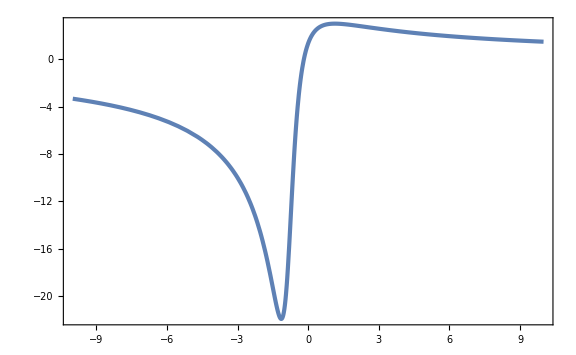

```mathematica
Plot[𝒟[x]/.{γ->-3.178,δ->2.429,μ->-0.842,σ->0.454},{x,-10,10}]
```

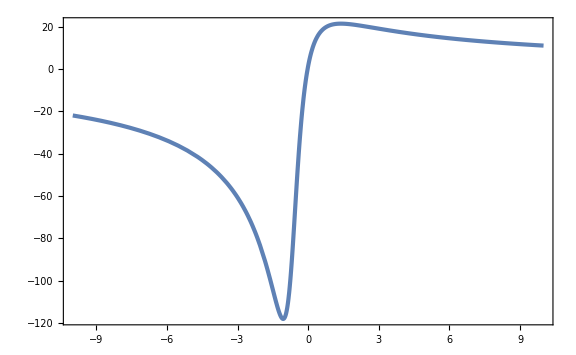

```mathematica
Plot[𝒟[x]/.{γ->-7.06,δ->6.65,μ->-0.682,σ->0.53},{x,-10,10}]
```

```mathematica
16/(2 (10^7)^2)//N
```

8.×10^-14

```mathematica
M=10^-2;
ϕc=Sqrt[2]M;
```

## quadratic

```mathematica
Π2=100;
μ1=Π2/(M^2 ϕc);μ1//N
Λ=(As 12 π^2 μ1^-2)^(1/4)/.{As->2.1 10^-9}
ψr=Sqrt[(Λ^4 Sqrt[Π2])/(48Sqrt[2 π^3])]
μ2=10.7;
```

7.07107×10^7

2.65572×10^-6

1.14716×10^-12

### N = 2

```mathematica
ys={y1,y2};
pys={py1,py2};
wys={wy1,wy2};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

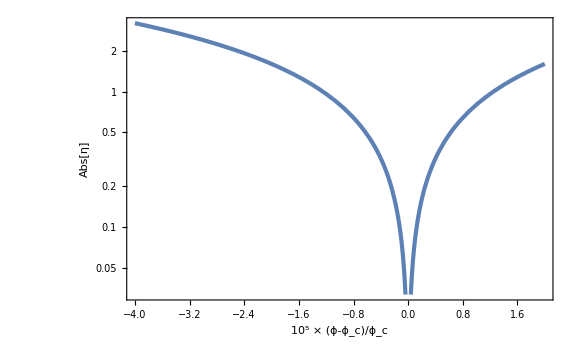

```mathematica
LogPlot[Abs[ηr[ϕc(1+dx 10^-5),0]],{dx,-4,2},GridLines->{None,{2}},FrameLabel->{Row[{"10^5 × ",(ϕ-Subscript[ϕ, "c"])/Subscript[ϕ, "c"]}],Abs[η]}]
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc(*+15/μ1*),0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=25;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

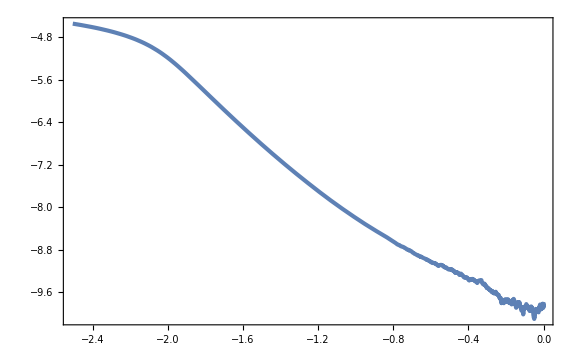

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^5,Log10[Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M]},{NN,0,Nf}]
```

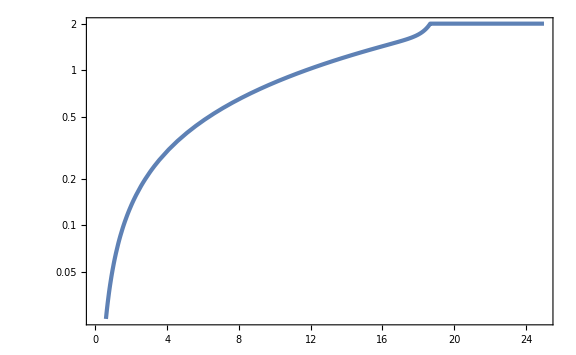

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=25;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01}(*,10^3*)]["LastValues"],10^4]//Flatten;//AbsoluteTiming
```

$Aborted

```mathematica
Export["N=2_1e4.csv",dNsampling];
```

```mathematica
dNsamplingN2=Import["N=2_1e7.csv"]//Flatten;
```

```mathematica
Mean[dNsamplingN2]
Variance[dNsamplingN2-Mean[dNsamplingN2]]
```

19.0566

0.163632

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc+15/μ1,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc,x'[0]==0,NN[0]==0,WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];"StopIntegration"]},{x[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
Nend-Mean[dNsamplingN2]
```

2.11494

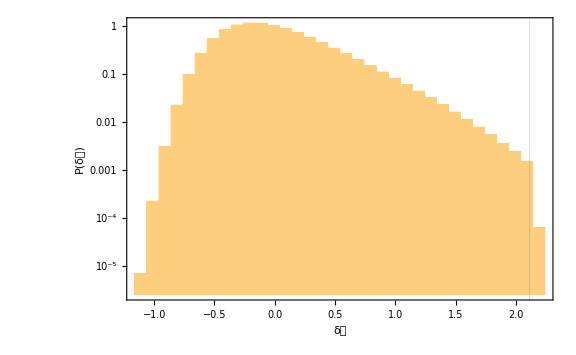

```mathematica
Histogram[dNsamplingN2-Mean[dNsamplingN2],{-1.16,2.26,0.1},{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==2}},PlotRange->Full,GridLines->{{Nend-Mean[dNsamplingN2]},None}]
```

```mathematica
dNpartN2=Partition[dNsamplingN2,10^6];
```

```mathematica
binListN2=HistogramList[dNsamplingN2-Mean[dNsamplingN2],{-1.16,2.26,0.1},"PDF"][[1]];
```

```mathematica
HistoListN2=Table[HistogramList[dNpartN2[[i]]-Mean[dNpartN2[[i]]],{binListN2},"PDF"][[2]],{i,Length[dNpartN2]}]//Transpose;
```

```mathematica
JackHistoN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]±StandardDeviation[HistoListN2[[i]]]/Sqrt[10]},{i,Length[binListN2]-1}];
JackHistoWOEN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]},{i,Length[binListN2]-1}];
JackHistoErrN2=Table[StandardDeviation[HistoListN2[[i]]]/Sqrt[10],{i,Length[binListN2]-1}];
JackHistoLog=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Log[Mean[HistoListN2[[i]]]]},{i,Length[binListN2]-1}];
```

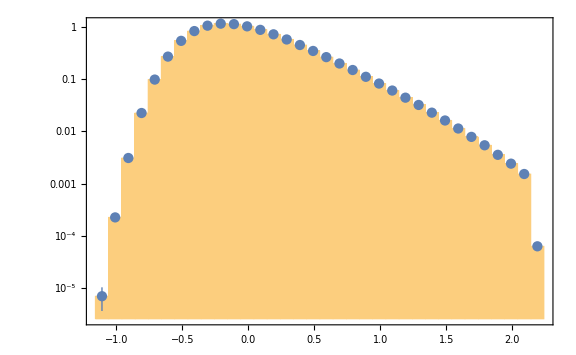

```mathematica
Show[Histogram[dNsamplingN2-Mean[dNsamplingN2],{binListN2},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN2,Joined->False]]
```

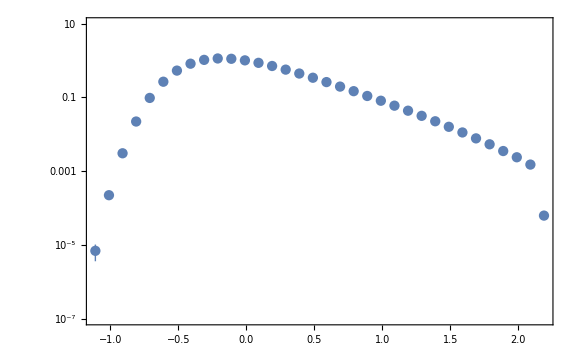

```mathematica
ListLogPlot[JackHistoN2,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
SUfitN2=NonlinearModelFit[JackHistoWOEN2,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/JackHistoErrN2^2*),MaxIterations->1000]
```

FittedModel[(0.969144 ⅇ^(-1/2 («1»)^2))/(√(0.206543+(«19»+x)^2))]

```mathematica
SUfitN2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | -3.17804 | 0.0892459 | -35.61 | 4.18656×10^-26
δ | 2.42928 | 0.0245362 | 99.0081 | 2.67409×10^-39
μ | -0.842461 | 0.0131011 | -64.3044 | 1.05617×10^-33
σ | 0.45447 | 0.00599965 | 75.7494 | 7.98551×10^-36

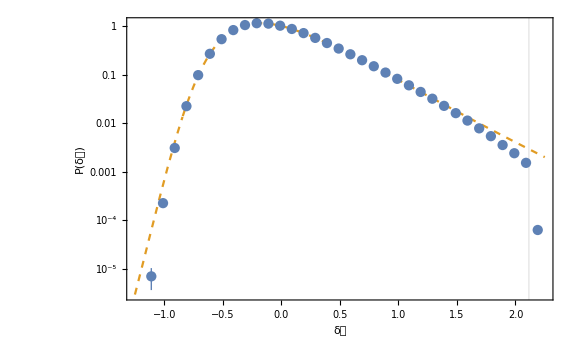

```mathematica
Show[LogPlot[Normal[SUfitN2],{x,-1.25,2.25},PlotStyle->{Color[2],Dashed},GridLines->{{Nend-Mean[dNsamplingN2]},None},FrameLabel->{{P[δ𝒩],None},{δ𝒩,Row[{"Quadratic ",n==2}]}}],ListLogPlot[JackHistoN2,Joined->False]]
```

```mathematica
D[Log[Normal[SUfitN2]], x]/.{x->1}
```

-2.99799

### N = 15

```mathematica
ys={y1,y2,y3,y4,y5,y6,y7,y8,y9,y10,y11,y12,y13,y14,y15};
pys={py1,py2,py3,py4,py5,py6,py7,py8,py9,py10,py11,py12,py13,py14,py15};
wys={wy1,wy2,wy3,wy4,wy5,wy6,wy7,wy8,wy9,wy10,wy11,wy12,wy13,wy14,wy15};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc(*+15/μ1*),0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=25;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

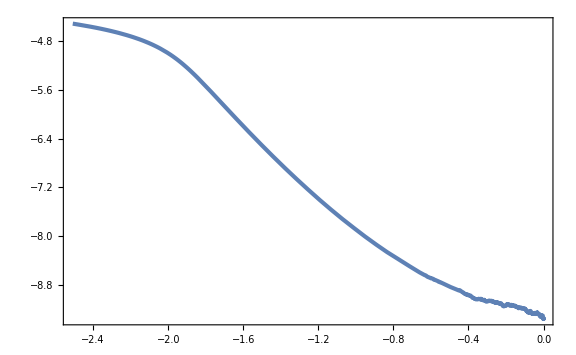

```mathematica
ParametricPlot[{(sample["PathFunction"][NN][[1]]-ϕc)/ϕc 10^5,Log10[Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M]},{NN,0,Nf}]
```

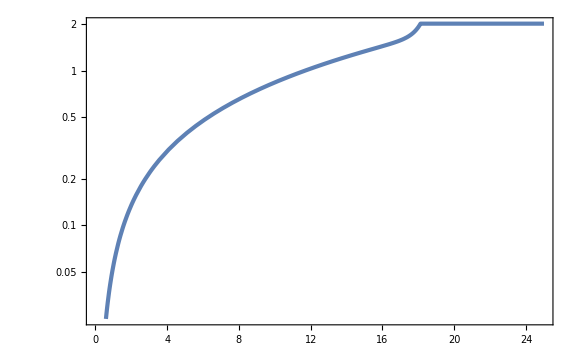

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=25;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],{i,10^4}]//Flatten;//AbsoluteTiming
```

{24974.4,Null}

```mathematica
Export["N=15_1e7.csv",dNsampling];
```

```mathematica
dNsamplingN15=Import["N=15_1e7.csv"]//Flatten;
```

```mathematica
Mean[dNsamplingN15]
Variance[dNsamplingN15-Mean[dNsamplingN15]]
```

18.1552

0.0169603

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc,x'[0]==0,NN[0]==0,WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];"StopIntegration"]},{x[t],NN[t]},{t,0,tf}][[1]];
```

```mathematica
Nend-Mean[dNsamplingN15]
```

3.0163

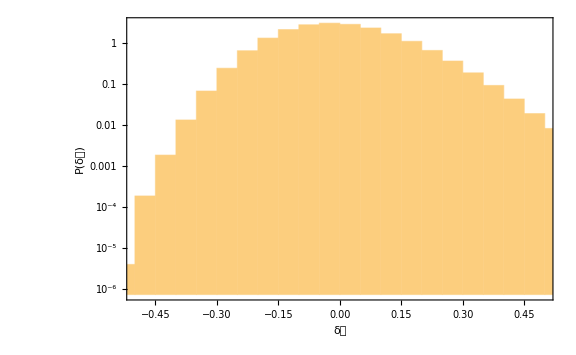

```mathematica
Histogram[dNsamplingN15-Mean[dNsamplingN15],Automatic,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==15}}]
```

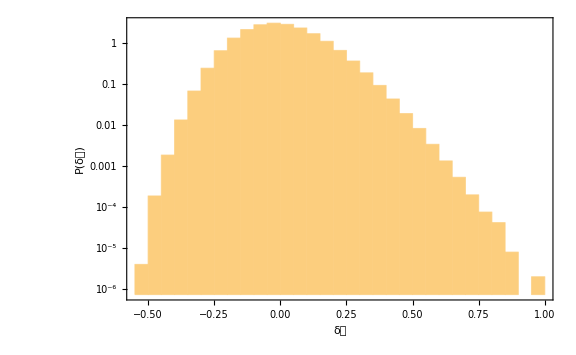

```mathematica
Histogram[dNsamplingN15-Mean[dNsamplingN15],30,{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,"waterfall = 15"}},PlotRange->Full]
```

```mathematica
dNpartN15=Partition[dNsamplingN15,10^6];
```

```mathematica
binListN15=HistogramList[dNsamplingN15-Mean[dNsamplingN15],30,"PDF"][[1]];
```

```mathematica
binListN15
```

{-11/20,-1/2,-9/20,-2/5,-7/20,-3/10,-1/4,-1/5,-3/20,-1/10,-1/20,0,1/20,1/10,3/20,1/5,1/4,3/10,7/20,2/5,9/20,1/2,11/20,3/5,13/20,7/10,3/4,4/5,17/20,9/10,19/20,1}

```mathematica
HistoListN15=Table[HistogramList[dNpartN15[[i]]-Mean[dNpartN15[[i]]],{binListN15},"PDF"][[2]],{i,Length[dNpartN15]}]//Transpose;
```

```mathematica
JackHistoN15=Table[If[Mean[HistoListN15[[i]]]>0,{(binListN15[[i]]+binListN15[[i+1]])/2,Mean[HistoListN15[[i]]]±StandardDeviation[HistoListN15[[i]]]/Sqrt[10]},Nothing],{i,Length[binListN15]-1}];
JackHistoWOEN15=Table[If[Mean[HistoListN15[[i]]]>0,{(binListN15[[i]]+binListN15[[i+1]])/2,Mean[HistoListN15[[i]]]},Nothing],{i,Length[binListN15]-1}];
JackHistoErrN15=Table[If[Mean[HistoListN15[[i]]]>0,StandardDeviation[HistoListN15[[i]]]/Sqrt[10],Nothing],{i,Length[binListN15]-1}];
```

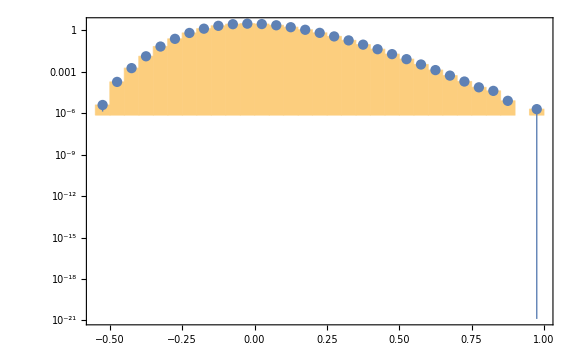

```mathematica
Show[Histogram[dNsamplingN15-Mean[dNsamplingN15],{binListN15},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN15,Joined->False]]
```

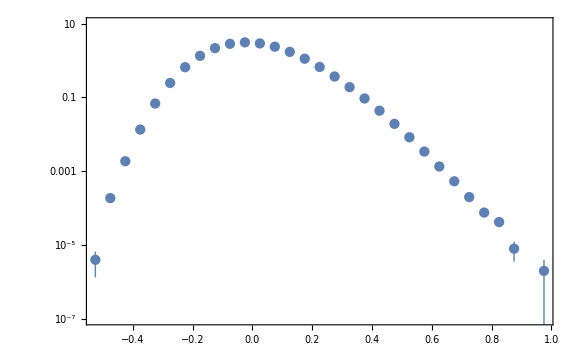

```mathematica
ListLogPlot[JackHistoN15,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x]
```

(ⅇ^(-1/2 (γ+δ ArcSinh[(x-μ)/σ])^2) δ)/(√(2 π) √((x-μ)^2+σ^2))

```mathematica
SUfitN15=NonlinearModelFit[JackHistoWOEN15,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/JackHistoErrN15^2*),MaxIterations->1000]
```

FittedModel[(2.65391 ⅇ^(-1/2 («1»)^2))/(√(0.281305+(0.682221+x)^2))]

```mathematica
SUfitN15["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | -7.06086 | 0.181273 | -38.9515 | 1.37653×10^-24
δ | 6.65237 | 0.0601637 | 110.571 | 2.74582×10^-36
μ | -0.682221 | 0.0118881 | -57.3871 | 6.50057×10^-29
σ | 0.530382 | 0.00286451 | 185.156 | 4.21518×10^-42

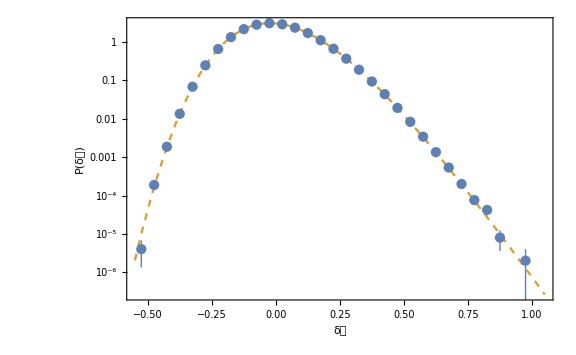

```mathematica
Show[LogPlot[Normal[SUfitN15],{x,-0.55,1.05},PlotStyle->{Color[2],Dashed},FrameLabel->{{P[δ𝒩],None},{δ𝒩,Row[{"Quadratic ",n==15}]}}],ListLogPlot[JackHistoN15,Joined->False]]
```

```mathematica
D[Log[Normal[SUfitN15]], x]/.{x->1}
```

-20.8629

## cubic

```mathematica
Π2=11^2;
μ1=Π2/(M^2 ϕc);μ1//N
Λ=(As 12 π^2 μ1^-2)^(1/4)/.{As->2.1 10^-9}
ψr=Sqrt[(Λ^4 Sqrt[Π2])/(48Sqrt[2 π^3])]
μ2=6.8;
μ3=0.0375;
```

8.55599×10^7

2.41429×10^-6

9.94342×10^-13

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc,0];
tf=200/Hxin;
tc=0;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc+30/μ1,x'[0]==0,NN[0]==0,WhenEvent[x[t]==ϕc,tc=t;"StopIntegration"]},{x[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];//Quiet
```

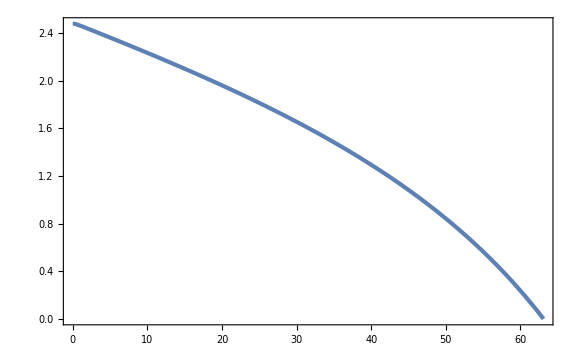

```mathematica
ParametricPlot[{NN[t]/.hillsol,(x[t]-ϕc)/ϕc 10^5/.hillsol},{t,0,tc}]
```

```mathematica
xsol[t_]=x[t]/.hillsol;
Nsol[t_]=NN[t]/.hillsol;
```

```mathematica
tCMB=t/.FindRoot[Nsol[tc]-Nsol[t]==50-18.4,{t,tc/10}];//Quiet
Nsol[tc]-Nsol[tCMB]
```

31.6

```mathematica
1+2 Vx''[xsol[tCMB]]/Vx[xsol[tCMB]]
```

0.965157

### N = 2

```mathematica
ys={y1,y2};
pys={py1,py2};
wys={wy1,wy2};
ny=Length[ys];
ysN=Table[ys[[i]][NN],{i,ny}];
pysN=Table[pys[[i]][NN],{i,ny}];
```

```mathematica
V[x_,ys_]:=Λ^4((1-(ys.ys)/M^2)^2+2(x^2 ys.ys)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3)
```

```mathematica
Vr[x_,yr_]=Λ^4((1-yr^2/M^2)^2+2(x^2 yr^2)/(M^2 ϕc^2)+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
ηr[x_,yr_]=D[D[Vr[x,yr], yr], yr]/Vr[x,yr];
```

```mathematica
LogPlot[Abs[ηr[ϕc(1+dx 10^-5),0]],{dx,-4,2},GridLines->{None,{2}},FrameLabel->{Row[{"10^5 × ",(ϕ-Subscript[ϕ, "c"])/Subscript[ϕ, "c"]}],Abs[η]}]
```

-Graphics-

```mathematica
H[x_,ys_,px_,pys_]:=Sqrt[(px^2/2+(pys.pys)/2+V[x,ys])/3]
```

```mathematica
EoMx={ⅆx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](px[NN]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwx[NN]),
ⅆpx[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3px[NN]-D[V[x[NN],ysN], x[NN]]/H[x[NN],ysN,px[NN],pysN])ⅆNN};
EoMy=Flatten[Table[{ⅆysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](pysN[[i]]/H[x[NN],ysN,px[NN],pysN] ⅆNN+H[x[NN],ysN,px[NN],pysN]/(2π)ⅆwys[[i]][NN]),
ⅆpysN[[i]]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2](-3pysN[[i]]-D[V[x[NN],ysN], ysN[[i]]]/H[x[NN],ysN,px[NN],pysN])ⅆNN},{i,ny}]];
```

```mathematica
IV=Flatten[{ϕc,0,Table[ψr,{i,ny}],Table[0,{i,ny}],0}];
```

```mathematica
prob=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Flatten[{x[NN],px[NN],ysN,pysN,Ninf[NN]}],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
```

```mathematica
Nf=25;
sample=RandomFunction[prob,{0,Nf,0.01}];
```

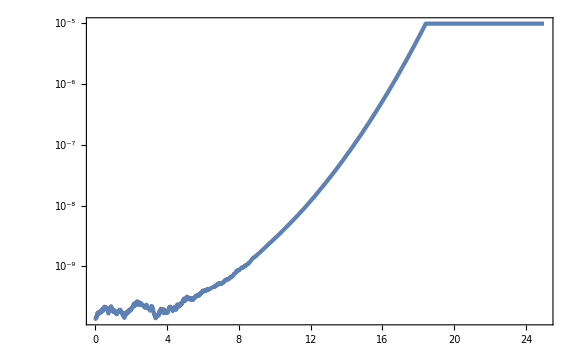

```mathematica
LogPlot[Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]/M,{NN,0,Nf}]
```

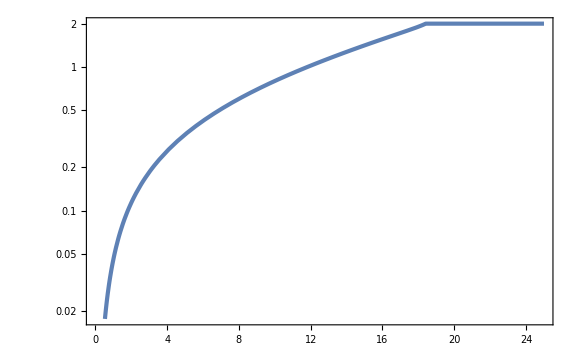

```mathematica
LogPlot[Abs[ηr[sample["PathFunction"][NN][[1]],Sqrt[Sum[(sample["PathFunction"][NN][[2+i]])^2,{i,ny}]]]],{NN,0,Nf}]//Quiet
```

```mathematica
deltaN=ItoProcess[Flatten[{EoMx,EoMy,ⅆNinf[NN]==UnitStep[ηr[x[NN],Sqrt[ysN.ysN]]+2]ⅆNN}],Ninf[NN],{Flatten[{x,px,ys,pys,Ninf}],IV},NN,Flatten[{wx\[Distributed]WienerProcess[],Table[wys[[i]]\[Distributed]WienerProcess[],{i,ny}]}]];
Nf=25;
dNsampling=ParallelTable[RandomFunction[deltaN,{0,Nf,0.01},10^3]["LastValues"],10^4]//Flatten;//AbsoluteTiming
```

{14014.1,Null}

```mathematica
Export["N=2_cubic.csv",dNsampling];
```

```mathematica
dNsamplingN2=Import["N=2_cubic.csv"]//Flatten;
```

```mathematica
mean=Mean[dNsamplingN2]
Variance[dNsamplingN2-Mean[dNsamplingN2]]
```

18.3691

0.0152025

```mathematica
Vx[x_]=Λ^4(1+(x-ϕc)/μ1-(x-ϕc)^2/μ2^2+(x-ϕc)^3/μ3^3);
Hx[x_,p_]=Sqrt[(p^2/2+Vx[x])/3];
ηrx[x_]=ηr[x,0];
```

```mathematica
Hxin=Hx[ϕc,0];
tf=50/Hxin;
hillsol=NDSolve[{x''[t]+3Hx[x[t],x'[t]]x'[t]+Vx'[x[t]]==0,NN'[t]==Hx[x[t],x'[t]],x[0]==ϕc,x'[0]==0,NN[0]==0,WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];
xend=x[t];"StopIntegration"]},{x[t],NN[t]},{t,0,tf},WorkingPrecision->30][[1]];
```

NDSolve::precw: The precision of the differential equation ({{3.3975×10^-23 (Power[«2»]/60500000-0.0432526 Plus[«2»]+56888.9 Power[«2»])+√3 x'[t] √(Times[«2»]+Times[«2»])+x''[t]==0,NN'[t]==(√(3.3975×10^-23 Plus[«4»]+1/2 Power[«2»]))/(√3),x[0]==1/(50 √2),x'[0]==0,NN[0]==0},{},{},{},{WhenEvent[ηrx[x[t]]==-2,Nend=NN[t];xend=x[t];StopIntegration]}}) is less than WorkingPrecision (30.).

```mathematica
1-xend/ϕc
```

0.00002500031250781254854683243

```mathematica
Nend
```

18.572369325688557619615247937

```mathematica
Nend-Mean[dNsamplingN2]
```

0.203222

```mathematica
HistogramList[dNsamplingN2-Mean[dNsamplingN2],30]
```

{{-3/5,-29/50,-14/25,-27/50,-13/25,-1/2,-12/25,-23/50,-11/25,-21/50,-2/5,-19/50,-9/25,-17/50,-8/25,-3/10,-7/25,-13/50,-6/25,-11/50,-1/5,-9/50,-4/25,-7/50,-3/25,-1/10,-2/25,-3/50,-1/25,-1/50,0,1/50,1/25,3/50,2/25,1/10,3/25,7/50,4/25,9/50,1/5,11/50},{1,0,4,17,25,83,228,497,1019,2129,4172,7192,12616,20457,32173,47976,69909,96245,129252,167129,211636,256457,306540,355319,402732,446092,485233,518864,541781,558882,568302,568203,560855,548518,529903,504907,478133,447594,417648,385894,315383}}

```mathematica
HistogramList[dNsamplingN2-Mean[dNsamplingN2],{{-100,0,100}}]
```

{{-100,0,100},{4674660,5325340}}

```mathematica
(HistogramList[dNsamplingN2-Mean[dNsamplingN2],{{-100,0,100}}][[2,2]])/10^7//N
```

0.532534

```mathematica
Select[dNsamplingN2,-3/5<=#-mean<-29/50&]
```

{17.78}

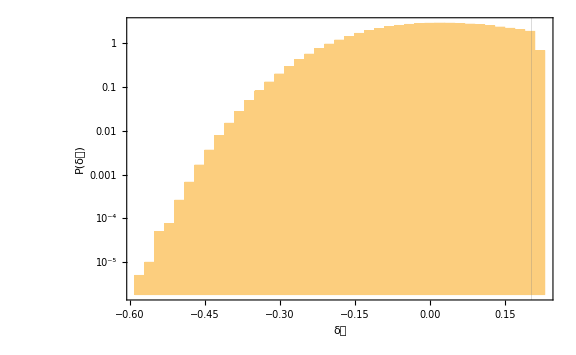

```mathematica
Histogram[dNsamplingN2-Mean[dNsamplingN2],{-0.59,0.23,0.02},{"Log","PDF"},FrameLabel->{{P[δ𝒩],None},{δ𝒩,n==2}},PlotRange->Full,GridLines->{{Nend-Mean[dNsamplingN2]},None}]
```

```mathematica
dNpartN2=Partition[dNsamplingN2,10^6];
```

```mathematica
binListN2=HistogramList[dNsamplingN2-Mean[dNsamplingN2],{-0.59,0.23,0.02},"PDF"][[1]];
```

```mathematica
HistoListN2=Table[HistogramList[dNpartN2[[i]]-Mean[dNpartN2[[i]]],{binListN2},"PDF"][[2]],{i,Length[dNpartN2]}]//Transpose;
```

```mathematica
JackHistoN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]±StandardDeviation[HistoListN2[[i]]]/Sqrt[10]},{i,Length[binListN2]-1}];
JackHistoWOEN2=Table[{(binListN2[[i]]+binListN2[[i+1]])/2,Mean[HistoListN2[[i]]]},{i,Length[binListN2]-1}];
JackHistoErrN2=Table[StandardDeviation[HistoListN2[[i]]]/Sqrt[10],{i,Length[binListN2]-1}];
```

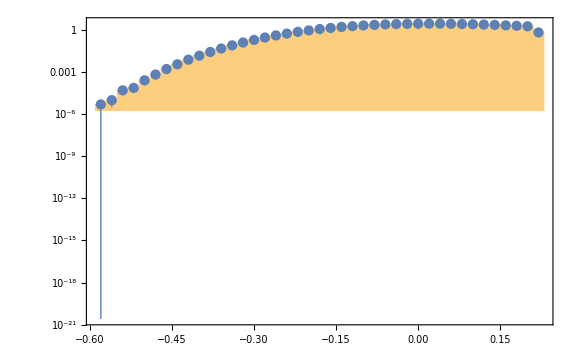

```mathematica
Show[Histogram[dNsamplingN2-Mean[dNsamplingN2],{binListN2},{"Log","PDF"},PlotRange->Full],ListLogPlot[JackHistoN2,Joined->False]]
```

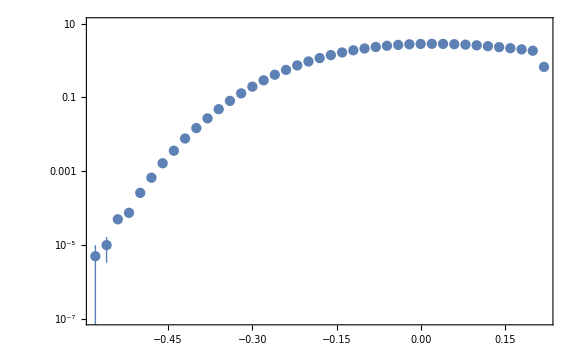

```mathematica
ListLogPlot[JackHistoN2,Joined->False,PlotRange->{10^-7,10}]
```

```mathematica
SUfitN2=NonlinearModelFit[JackHistoWOEN2,PDF[JohnsonDistribution["SU",γ,δ,μ,σ],x],{γ,δ,μ,σ},x(*,Weights->1/Drop[JackHistoErrN2,-1]^2*),MaxIterations->1000]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

FittedModel[(6.72471 ⅇ^(-1/2 («1»)^2))/(√(0.00213536+(-2.35494+x)^2))]

```mathematica
SUfitN2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
γ | 77.7898 | 572241. | 0.000135939 | 0.999892
δ | 16.8563 | 221.16 | 0.076218 | 0.939656
μ | 2.35494 | 61.5898 | 0.0382359 | 0.969705
σ | 0.04621 | 1565.04 | 0.0000295264 | 0.999977

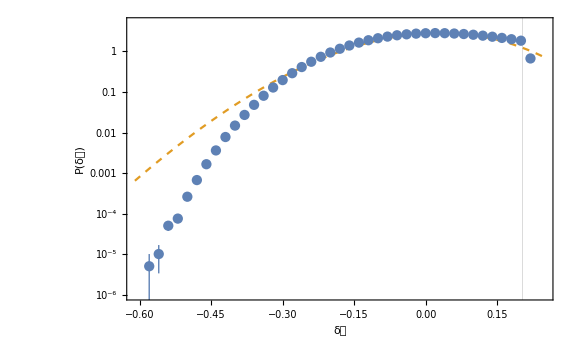

```mathematica
Show[LogPlot[Normal[SUfitN2],{x,-0.61,0.25},PlotStyle->{Color[2],Dashed},GridLines->{{Nend-Mean[dNsamplingN2]},None},FrameLabel->{{P[δ𝒩],None},{δ𝒩,Row[{"Cubic ",n==2}]}},PlotRange->{10^-6,5}],ListLogPlot[JackHistoN2,Joined->False]]
```

### Tada & Yamada

```mathematica
χ2=Log[(M Sqrt[ϕc])/(2ψr Sqrt[μ1])]
```

11.0767

```mathematica
Sqrt[Π2](Sqrt[χ2]/2+c/(4Sqrt[χ2]))/.{c->1}
Π2/(12 μ2^2)(χ2+c)/.{c->1}
Sqrt[Π2]^3/(32μ1 μ3^3)(Sqrt[χ2]^3+(3c)/2 Sqrt[χ2])/.{c->1}
Nc=Sqrt[Π2](Sqrt[χ2]/2+c/(4Sqrt[χ2]))-Π2/(12 μ2^2)(χ2+c)-Sqrt[Π2]^3/(32μ1 μ3^3)(Sqrt[χ2]^3+(3c)/2 Sqrt[χ2])/.{c->1}
```

19.1312

2.63351

0.385866

16.1118

```mathematica
0.013Nc(χ2/10)^(-3/2)(1-Nc/(3 μ2^2)-Nc^2/(2μ1 μ3^3))
Nc/(3 μ2^2)
Nc^2/(2μ1 μ3^3)
```

0.153632

0.116146

0.0287671

```mathematica
N1s//N
N2s/.{N1->N1s}
N3s/.{N1->N1s,N2->N2s}/.{N1->N1s}
N1s+N2s+N3s/.{N1->N1s,N2->N2s}/.{N1->N1s}
```

30.25

4.53155

-2.95271

31.8288

```mathematica
Solve[-Π2/4==-NN-NN^2/μ2^2-ϕc/μ3^3 1/(μ1 ϕc)NN^3,NN]
```

{{NN→-58.7476-58.318 ⅈ},{NN→-58.7476+58.318 ⅈ},{NN→19.9184}}